# Data Science and Machine Learning

## Lab session 09: Text analytics

## Accessing text

### Import text

You can import from a variety of sources, including...

Wikipedia Articles:

```mathematica
alKhwarizmi = WikipediaData["Muhammad ibn Musa al-Khwarizmi"];
```

Webpages, e.g. from Stanford Encyclopedia of Philosophy

```mathematica
publicGood = Import["https://plato.stanford.edu/entries/public-goods/", "Plaintext"];
```

Books, e.g. "An Inquiry into the Nature and Causes of the Wealth of Nations" by Adam Smith, from the Project Gutenberg:

```mathematica
wealthofNations = Import["https://www.gutenberg.org/cache/epub/38194/pg38194.txt"];
```

From PDF files:

```mathematica
circularEco=Import["MGT-492/Week_09_Text-analytics/E4S_Circular_Economy.pdf", "Plaintext"];
```

Tweets - you need a Twitter account:

```mathematica
twitter=ServiceConnect["Twitter","New"];
twitter["UserData","Username"->"elonmusk"]
```

And much more e.g. subtitles from video

Since text are larges objects, to visualize your data you can display a Snippet or generate a WordCloud:

Muḥammad ibn Mūsā al-Khwārizmī (Persian: محمد بن موسی خوارزمی‎, romanized:
Moḥammad ben Musā Khwārazmi; c. 780 – c. 850), or al-Khwarizmi and formerly
Latinized as Algorithmi, was a Persian polymath who produced vastly influential
works in mathematics, astronomy, and geography. Around 820 CE he was appointed

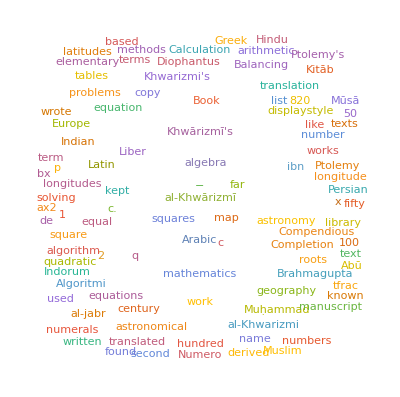

```mathematica
Snippet[alKhwarizmi,4]
WordCloud[alKhwarizmi]
```

### Extracting sentences

TextSentences gives a list of the identified sentences from a text (string).

```mathematica
wealthofNationsSentences = TextSentences[wealthofNations];
wealthofNationsSentences[[160]]
```

Adam Smith, the celebrated author of 'An Inquiry into the Nature and
Causes of the Wealth of Nations,' was born in the town of Kirkaldy, on
the 5th of June 1723.

Sentences may not be precisely identified in unstructured text:

```mathematica
circularEcoSentences = TextSentences[circularEco];
circularEcoSentences[[5]]
```

Bending the line: Towards a Circular Economy | E4S White Paper | 3
Table of Contents
Executive Summary.............................................................................................................................................................4
1 Introduction .......................................................................................................................................................................6
2 The Linear Economy and its Environmental Impact........................................................................................8
2.1 The linear economy has pushed the planet out of its boundaries .................................................9
2.2 Resource use is a at the heart of the problem.......................................................................................11
2.3 Market failures in the linear economy........................................................................................................12
2.4 Correcting environmental market failures.................................................................................................13
2.5 Summing up............................................................................................................................................................17
3 Circular Economy: a Sustainable Alternative.....................................................................................................18
3.1 Principles of a CE..................................................................................................................................................20
3.2 Differences between the linear and circular economy ........................................................................21
3.3 Possible benefits of the CE for environment and economy .............................................................22
3.4 Open questions .....................................................................................................................................................23
4 The Circular Economy in the Global Context...................................................................................................26
5 Bending the Line: Policies to Transition to a Circular Economy..............................................................29
5.1 Policies.......................................................................................................................................................................31
5.1.1 Move towards the use of renewable energy and resources....................................................31
5.1.2 Recycle materials at the end of life and use as inputs...............................................................32
5.1.3 Increase the lifespan of products .........................................................................................................33
5.1.4 Increase the use intensity of products through sharing............................................................35
5.1.5 Decrease waste..............................................................................................................................................36
5.2 Circularity indicators............................................................................................................................................37
6 Conclusion........................................................................................................................................................................39
References ............................................................................................................................................................................40
Contact...................................................................................................................................................................................43
About E4S .............................................................................................................................................................................43
Bending the line: Towards a Circular Economy | E4S White Paper | 4
Executive Summary
English
The world is today operating in a linear 
economy that extracts natural resources, 
produces energy or goods which are 
disposed in the form of pollution or waste. 
This “take, make, waste” system has 
generated prosperity and wealth in many 
parts of the world, but has also polluted the 
planet and the atmosphere.

In such cases, you need to manipulate your text to extract the information you are looking for.
For instance, let's extract the English Executive Summary of the E4S white paper "Bending the line: Towards a Circular Economy"
Here is the procedure:
	1. We use StringSplit to split the 5th identified sentence in circularEcoSentences into two. As second argument (pattern for splitting), we use the keyword "English" because it just precedes the first sentence of the summary.
    	2. We use Prepend to merge the first sentence of the summary with the rest of the summary.
        	3. In the object we created, some sentences are not identified. We do another StringSplit, this time using "." as pattern for splitting. It is successful in this case because the symbol "." only appears at the end of sentences. Be careful, it is not always the case!

```mathematica
abstractEN1=StringSplit[circularEcoSentences[[5]],"English"][[2]];
abstractENraw = Prepend[circularEcoSentences[[6;;9]], abstractEN1];
abstractEN = Flatten @ StringSplit[abstractENraw,"."]
```

{
The world is today operating in a linear 
economy that extracts natural resources, 
produces energy or goods which are 
disposed in the form of pollution or waste, 
This “take, make, waste” system has 
generated prosperity and wealth in many 
parts of the world, but has also polluted the 
planet and the atmosphere,The 
consequences are climate change, the 
degradation of the environment, and loss of 
biodiversity,To avoid environmental 
catastrophes, there is an urgent need for a 
rapid transition away from the linear 
economy towards sustainable economic 
systems, 
The circular economy offers such an 
alternative,In its ideal form, a circular 
economy is a regenerative economic system 
that uses renewable energy and resources, 
reuses materials and products as long as 
possible, and recycles resources rather than 
disposing them as waste,This report 
analyzes the necessary conditions for a move 
towards a circular economy and examines
government policies that can foster the 
transition towards such a regenerative 
economy}

### Extracting words

TextWords gives a list of the identified words in a given "string".
Note that words returned by TextWords are identified structurally, and may not be dictionary words.

```mathematica
abstractENwordsRaw = TextWords[abstractEN]
```

{{The,world,is,today,operating,in,a,linear,economy,that,extracts,natural,resources,produces,energy,or,goods,which,are,disposed,in,the,form,of,pollution,or,waste},{This,take,make,waste,system,has,generated,prosperity,and,wealth,in,many,parts,of,the,world,but,has,also,polluted,the,planet,and,the,atmosphere},{The,consequences,are,climate,change,the,degradation,of,the,environment,and,loss,of,biodiversity},{To,avoid,environmental,catastrophes,there,is,an,urgent,need,for,a,rapid,transition,away,from,the,linear,economy,towards,sustainable,economic,systems},{The,circular,economy,offers,such,an,alternative},{In,its,ideal,form,a,circular,economy,is,a,regenerative,economic,system,that,uses,renewable,energy,and,resources,reuses,materials,and,products,as,long,as,possible,and,recycles,resources,rather,than,disposing,them,as,waste},{This,report,analyzes,the,necessary,conditions,for,a,move,towards,a,circular,economy,and,examines,government,policies,that,can,foster,the,transition,towards,such,a,regenerative,economy}}

Many words may not be helpful for your analysis,  for instance "the", "is", "a", "for", etc.
You can delete these words using DeleteStopWords:

```mathematica
abstractENwords = DeleteStopwords /@ abstractENwordsRaw
```

{{world,today,operating,linear,economy,extracts,natural,resources,produces,energy,goods,disposed,form,pollution,waste},{make,waste,system,generated,prosperity,wealth,parts,world,polluted,planet,atmosphere},{consequences,climate,change,degradation,environment,loss,biodiversity},{avoid,environmental,catastrophes,urgent,need,rapid,transition,away,linear,economy,towards,sustainable,economic,systems},{circular,economy,offers,alternative},{ideal,form,circular,economy,regenerative,economic,system,uses,renewable,energy,resources,reuses,materials,products,long,possible,recycles,resources,disposing,waste},{report,analyzes,necessary,conditions,move,towards,circular,economy,examines,government,policies,foster,transition,towards,regenerative,economy}}

## Manipulating strings

```mathematica
textCarbonRemoval = "Carbon removal, both CCUS (carbon capture in the industrial plant before it reaches the atmosphere) and NET (negative emissions, removing carbon from the air) could have an important role to play to reach net zero emissions. However, today carbon removal is experimental and small-scale, and is highly unlikely to scale beyond several percent of current emissions.";
```

### Delete string

StringDelete deletes substrings or patterns of a text/text.

For instance, let's remove the description of carbon removal in the string textCarbonRemoval. 
We need to specify the pattern to delete. Here, we remove everything between ", both CCUS" and the second parenthesis. 
	~~   	represents a sequence of strings
    	___  	stands for any sequence of expressions (BlankSequence)
See String Patterns for more details.

```mathematica
carbonRemoval = StringDelete[textCarbonRemoval, ", both"~~___ ~~ ")"]
```

Carbon removal could have an important role to play to reach net zero emissions. However, today carbon removal is experimental and small-scale, and is highly unlikely to scale beyond several percent of current emissions.

### Replace string

StringReplace  allows to replace substrings or patterns.

For instance, let's replace "could" by "will" in the previous text:

```mathematica
StringReplace[carbonRemoval, "could" -> "will"]
```

Carbon removal will have an important role to play to reach net zero emissions. However, today carbon removal is experimental and small-scale, and is highly unlikely to scale beyond several percent of current emissions.

### Split string

StringSplit allows to split a text/string into a list of substrings, according to a given pattern:

```mathematica
StringSplit[carbonRemoval,"."]
```

{Carbon removal could have an important role to play to reach net zero emissions, However, today carbon removal is experimental and small-scale, and is highly unlikely to scale beyond several percent of current emissions}

### Concatenate strings

StringRiffle creates a string by concatenating a list of strings, with spaces inserted between them.

```mathematica
carbonRemovalWords =TextWords[carbonRemoval]
```

{Carbon,removal,could,have,an,important,role,to,play,to,reach,net,zero,emissions,However,today,carbon,removal,is,experimental,and,small-scale,and,is,highly,unlikely,to,scale,beyond,several,percent,of,current,emissions}

```mathematica
StringRiffle @ carbonRemovalWords
```

Carbon removal could have an important role to play to reach net zero emissions However today carbon removal is experimental and small-scale and is highly unlikely to scale beyond several percent of current emissions

## Content analysis & extraction

### Text statistics: counting words

WordCount gives the total number of identified word in a string

```mathematica
WordCount[wealthofNations]
```

423533

WordCounts gives an association whose keys are the distinct words identified in "string", and whose values give the number of times those words appear in "string".

```mathematica
WordCounts[StringRiffle @ abstractENwords]
```

<|economy→6,circular→3,towards→3,waste→3,resources→3,regenerative→2,economic→2,transition→2,system→2,form→2,energy→2,linear→2,world→2,foster→1,policies→1,government→1,examines→1,move→1,conditions→1,necessary→1,analyzes→1,report→1,disposing→1,recycles→1,possible→1,long→1,products→1,materials→1,reuses→1,renewable→1,uses→1,ideal→1,alternative→1,offers→1,systems→1,sustainable→1,away→1,rapid→1,need→1,urgent→1,catastrophes→1,environmental→1,avoid→1,biodiversity→1,loss→1,environment→1,degradation→1,change→1,climate→1,consequences→1,atmosphere→1,planet→1,polluted→1,parts→1,wealth→1,prosperity→1,generated→1,make→1,pollution→1,disposed→1,goods→1,produces→1,natural→1,extracts→1,operating→1,today→1|>

Using the second argument, you can count "n-grams", i.e. sequence of n consecutive words:

```mathematica
WordCounts[StringRiffle @ abstractENwords, 2]
```

<|{circular,economy}→3,{linear,economy}→2,{regenerative,economy}→1,{towards,regenerative}→1,{transition,towards}→1,{foster,transition}→1,{policies,foster}→1,{government,policies}→1,{examines,government}→1,{economy,examines}→1,{towards,circular}→1,{move,towards}→1,{conditions,move}→1,{necessary,conditions}→1,{analyzes,necessary}→1,{report,analyzes}→1,{waste,report}→1,{disposing,waste}→1,{resources,disposing}→1,{recycles,resources}→1,{possible,recycles}→1,{long,possible}→1,{products,long}→1,{materials,products}→1,{reuses,materials}→1,{resources,reuses}→1,{energy,resources}→1,{renewable,energy}→1,{uses,renewable}→1,{system,uses}→1,{economic,system}→1,{regenerative,economic}→1,{economy,regenerative}→1,{form,circular}→1,{ideal,form}→1,{alternative,ideal}→1,{offers,alternative}→1,{economy,offers}→1,{systems,circular}→1,{economic,systems}→1,{sustainable,economic}→1,{towards,sustainable}→1,{economy,towards}→1,{away,linear}→1,{transition,away}→1,{rapid,transition}→1,{need,rapid}→1,{urgent,need}→1,{catastrophes,urgent}→1,{environmental,catastrophes}→1,{avoid,environmental}→1,{biodiversity,avoid}→1,{loss,biodiversity}→1,{environment,loss}→1,{degradation,environment}→1,{change,degradation}→1,{climate,change}→1,{consequences,climate}→1,{atmosphere,consequences}→1,{planet,atmosphere}→1,{polluted,planet}→1,{world,polluted}→1,{parts,world}→1,{wealth,parts}→1,{prosperity,wealth}→1,{generated,prosperity}→1,{system,generated}→1,{waste,system}→1,{make,waste}→1,{waste,make}→1,{pollution,waste}→1,{form,pollution}→1,{disposed,form}→1,{goods,disposed}→1,{energy,goods}→1,{produces,energy}→1,{resources,produces}→1,{natural,resources}→1,{extracts,natural}→1,{economy,extracts}→1,{operating,linear}→1,{today,operating}→1,{world,today}→1|>

You can also extract the frequency of a word in a string using WordFrequency:

```mathematica
WordFrequency[StringRiffle @ abstractENwords, "economy"]
```

0.0689655

### Content & entity identification

TextCases allows to extract all the expressions that are of a specified type.

For instance, let's extract the countries mentioned in the Wikipedia article about al-Khwarizmi

```mathematica
locationsAlKhwarizmi = TextCases[alKhwarizmi, "Country"]
```

{Persian,Persian,Portuguese,Indian,Persian,Iran,Turkmenistan,Uzbekistan,Iranian,China,India,Greek,Persian,Indian,Greek,Greek,Swiss,American,Indian,Indians,Indian,Greek,Indian,Indian,Indian,Indian,Spanish}

The above list is not uniform. Instead, we can directly extract the countries as entities using the interpretation capabilities of the Wolfram Language

```mathematica
locationsAlKhwarizmi = TextCases[alKhwarizmi, "Country" -> "Interpretation", VerifyInterpretation->True]
```

{Iran,Iran,Portugal,India,Iran,Iran,Turkmenistan,Uzbekistan,Iran,China,India,Greece,Iran,India,Greece,Greece,Switzerland,United States,India,India,India,Greece,India,India,India,India,Spain}

We can then work with our entities, visualizing the countries and the number of mentions with a GeoBubbleChart or a Dataset:

```mathematica
GeoBubbleChart[Counts[locationsAlKhwarizmi]]
```

-Graphics-

```mathematica
Dataset[ReverseSort@Counts[locationsAlKhwarizmi]]
```

### Content & entity extraction

TextContents gives a dataset of information about entities, dates, quantities and other content-related elements found in a text.

```mathematica
wealthofNationsSentences[[160]]
```

Adam Smith, the celebrated author of 'An Inquiry into the Nature and
Causes of the Wealth of Nations,' was born in the town of Kirkaldy, on
the 5th of June 1723.

```mathematica
TextContents[wealthofNationsSentences[[160]], VerifyInterpretation->True]
```

TextContents::nlpnocf: No data available for TextCasesSpellings.

### Finding answers in text (Q&A)

FindTextualAnswer gives the substring of a text that best appears to answer a specified question.

```mathematica
FindTextualAnswer[publicGood, "What is the definition of a public good?"]
```

Kallhoff 2011: Ch. 2). According to her, a public good is one that satisfies the “basic availability condition” and the “open access condition”

### Searching text

TextSearchReport returns a structured report of files that contains the expression specified as second argument.

```mathematica
TextSearchReport["ExampleData/Text","cat"]
```

Clear::wrsym: Symbol TextSearch`LoadCLuceneLink is Protected.

### Understand the structure and meaning of text

TextStructure allows to display the grammatical structure of a sentence:

```mathematica
TextStructure["This is not a complex sentence."]
```

This
Determiner
Noun Phrase  is
Verbnot
Adverb  a
Determinercomplex
Adjectivesentence
Noun
Noun Phrase
Verb Phrase.
Punctuation
Sentence

You can get the definition of a word with WordDefinition

```mathematica
WordDefinition["computer"]
```

{a machine for performing calculations automatically,an expert at calculation (or at operating calculating machines)}

### Similarity between words/texts/vectors

EditDistance gives the number of one-element deletions, insertions, and substitutions required to transform one element into another.

```mathematica
EditDistance["economy","ecology"]
```

2

```mathematica
JaccardDissimilarity[{1,0,1,1,0},{1,1,0,1,1}]
```

3/5

Nearest gives the list of elements that are closest to a given expression.
Nearest[data] generates a NearestFunction[…] that can be applied repeatedly to different x.

```mathematica
nf=Nearest[DictionaryLookup[]]
```

NearestFunction[…]

We can apply our function to find the nearest words of, for instance, the word "ecology":

```mathematica
nf["ecology",6]
```

{ecology,apology,biology,colony,ecologic,economy}

We can create a graph displaying the nearest words of "ecology".
To do so, see how to create an association between "ecology" and its 4 nearest words.

```mathematica
Thread[#->nf[#,4]]&["ecology"]
```

{ecology→ecology,ecology→apology,ecology→biology,ecology→colony}

We can repeat this operation to identify the 4 nearest neighbors of the neighbors.
Nest allows to apply a function several times. The first argument is the function, the second the argument, the third the number of times you wish to apply your function (i.e. the nesting level).

```mathematica
ecologyNeighbors = Nest[Flatten[Thread[#->nf[#,4]]&/@(Last/@#)]&,{""->"ecology"},3]
```

{ecology→ecology,ecology→apology,ecology→biology,ecology→colony,apology→apology,apology→analogy,apology→apologia,apology→auxology,biology→biology,biology→apology,biology→billowy,biology→biologic,colony→colony,colony→colon,colony→colons,colony→clone,apology→apology,apology→analogy,apology→apologia,apology→auxology,analogy→analogy,analogy→analog,analogy→analogs,analogy→anally,apologia→apologia,apologia→apologias,apologia→apologies,apologia→apologist,auxology→auxology,auxology→apology,auxology→audiology,auxology→doxology,biology→biology,biology→apology,biology→billowy,biology→biologic,apology→apology,apology→analogy,apology→apologia,apology→auxology,billowy→billowy,billowy→billow,billowy→billows,billowy→willowy,biologic→biologic,biologic→biological,biologic→biologist,biologic→biology,colony→colony,colony→colon,colony→colons,colony→clone,colon→colon,colon→Colon,colon→colons,colon→colony,colons→colons,colons→colon,colons→colony,colons→colors,clone→clone,clone→alone,clone→cloned,clone→clones}

Finally, you can do a GraphPlot, where a link between two words is created if one belongs to the 4 nearest neighbors of the other.

```mathematica
GraphPlot[ecologyNeighbors,PlotTheme->"ClassicDiagram",VertexSize->{.2,.2}]
```

-Graphics-

## Applications

### Language identification

```mathematica
DynamicModule[{text=""},
 Column[ {
     InputField[Dynamic[text], String, ContinuousAction->True,FieldHint->"Enter a string"],
       Dynamic[Classify["Language", text, "TopProbabilities"]]
      }
  ]
 ]
```

Notice here the use of DynamicModule and Dynamic as well as InputField to create interactive content!

```mathematica
InputField[]
```

```mathematica
DynamicModule[{number=x},{InputField[Dynamic[number], Number],Dynamic[number^2]}]
```

### Topic Modelling - Understand the topic of a text

```mathematica
Classify["FacebookTopic", {"I bought a new computer", "happy birthday", "this dress looks nice"}]
```

{Technology,SpecialOccasions,Fashion}

### Text Classification - Spam Detection

```mathematica
cSpam = Classify["Spam"];
```

```mathematica
cSpam["Dear Sir, I feel you should send 1M dollars to my account. Yours truly."]
```

True

```mathematica
cSpam["I thought that latest song of Florence + The Machine was amazing"]
```

False

### Text Classification - Sentiment Analysis

```mathematica
cSentiment = Classify["Sentiment"];
```

```mathematica
cSentiment["I thought that latest song of Florence + The Machine was amazing"]
```

Positive

```mathematica
cSentiment["I didn't like the last move of Google"]
```

Negative

## Useful Links

Text Manipulation functions

Text Analysis functions